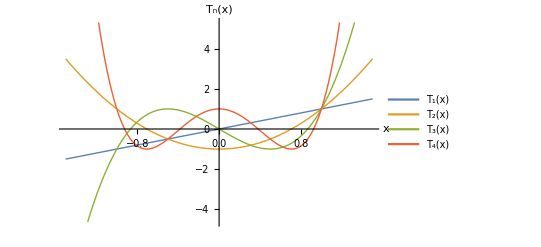

```mathematica
ClearAll[a, ChebychevFig1]
a = Table[i,{i,4}];
ChebychevFig1 = Plot[ChebyshevT[#,x] &/@ a // Evaluate ,{x,-1.5,1.5}, AxesLabel -> {x, "T_n(x)"}, 
PlotStyle-> Thick,PlotLegends -> Placed[ Row[{Subscript["T",#],"(x)"}] &/@ a, {Right,Bottom}]]
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/ece1229-antenna" ]
```

/Users/pjoot/project/figures/ece1229-antenna

```mathematica
peeters`exportForLatex["ChebychevFig1", ChebychevFig1]
```

{ChebychevFig1.eps,ChebychevFig1pn.png}